# Robots Day 7

## Quantitative Engineering Analysis - April 2019

## Exercise 10

```mathematica
Simplify[Eigenvalues[{{a,b},{b,-a}}]]
```

{-√(a^2+b^2),√(a^2+b^2)}

So, the point must be a saddle point if it’s a critical point!

## Exercise 11A

V(x,y)=log √(x^2+y^2)=log r

## Exercise 11B

```mathematica
Clear[V,x,y]
V[x_,y_]=Log[√(x^2+y^2)];
D[V[x,y], {x,2}]+D[V[x,y], {y,2}]
Simplify[%, x≠0 ||y≠0]
```

-(2 x^2)/((x^2+y^2)^2)-(2 y^2)/((x^2+y^2)^2)+2/(x^2+y^2)

0

## Exercise 11C

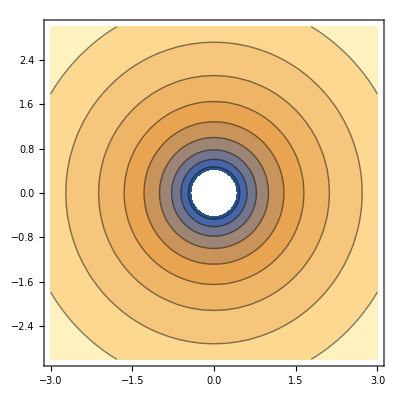

```mathematica
ContourPlot[V[x,y],{x,-3,3},{y,-3,3}]
```

```mathematica
Plot3D[V[x,y],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

## Exercise 12A

```mathematica
Clear[V,x,y]
V[x_,y_]=Log[√(x^2+y^2)]-Log[√((x-1)^2+y^2)];
D[V[x,y], {x,2}]+D[V[x,y], {y,2}]
Simplify[%, x≠0 ||y≠0]
```

(2 (-1+x)^2)/(((-1+x)^2+y^2)^2)+(2 y^2)/(((-1+x)^2+y^2)^2)-2/((-1+x)^2+y^2)-(2 x^2)/((x^2+y^2)^2)-(2 y^2)/((x^2+y^2)^2)+2/(x^2+y^2)

0

## Exercise 12B

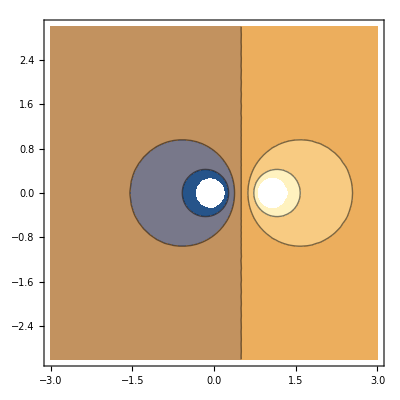

```mathematica
ContourPlot[V[x,y],{x,-3,3},{y,-3,3}]
```

```mathematica
Plot3D[V[x,y],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

## Exercise 13

```mathematica
Clear[V,x,y]
RotationMatrix[Pi/3]
V[x_,y_,m_,x0_,y0_]=Simplify[(∫Log[√((x-Subscript[x, 0]+x0)^2+(y-(m*Subscript[x, 0] )-y0)^2)]ⅆ Subscript[x, 0]/.{Subscript[x, 0]->3})-(∫Log[√((x-Subscript[x, 0]+x0)^2+(y-(m*Subscript[x, 0] )-y0)^2)]ⅆ Subscript[x, 0]/.{Subscript[x, 0]->-3})];
D[V[x,y], {x,2}]+D[V[x,y], {y,2}];
Simplify[%,x≠0||y≠0];
```

{{1/2,-(√3)/2},{(√3)/2,1/2}}

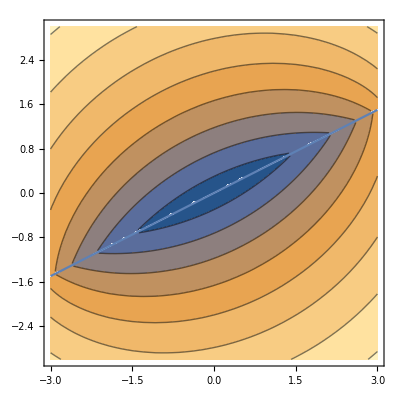

```mathematica
Show[ContourPlot[V[x,y, 0.5,0,0],{x,-3,3},{y,-3,3}],Plot[0.5*x,{x,-3,3}]]
```

```mathematica
Plot3D[V[x,y, 0.5,0,0],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

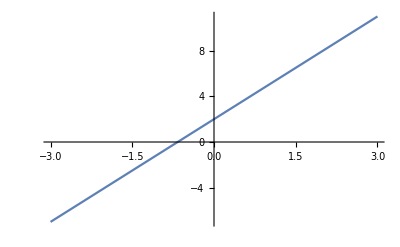

```mathematica
Plot[3*x+2,{x,-3,3}]
```

```mathematica
Manipulate[Show[ContourPlot[V[x,y, m,x0,y0],{x,-3,3},{y,-3,3}],Plot[(m*(x+x0) )+ y0,{x,-3,3}]],{m,-1,1},{x0,-3,3},{y0,-3,3}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.